```mathematica
fullsolvey=DSolve[{y'[t]==-A*(y[t])^2-B*y[t]+C*Exp[-γ*t], y[0]== d},y[t],t]
```

{{y[t]→(A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C)/γ] BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C)/γ] BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A B √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-√A B √C √(ⅇ^(-t γ)) BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+√A B √C BesselI[-1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+√A B √C BesselI[1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+√A B √C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+√A B √C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+B^2 BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-√A B √C BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A B √C BesselI[1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-B^2 BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-2 A B d BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+2 A B d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ])/(2 A (-√A √C BesselI[-1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A √C BesselI[1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-B BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+√A √C BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+√A √C BesselI[1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+B BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+2 A d BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]))}}

```mathematica
FullSimplify[%]
```

{{y[t]→(ⅇ^(-t γ) ((√A √C)/γ)^(-B/γ) ((√A √C √(ⅇ^(-t γ)))/γ)^(-B/γ) (-2 A C ((√A √C)/γ)^((2 B)/γ) Hypergeometric0F1Regularized[2-B/γ,(A C ⅇ^(-t γ))/γ^2] (A C Hypergeometric0F1Regularized[2+B/γ,(A C)/γ^2]+γ (γ Hypergeometric0F1Regularized[B/γ,(A C)/γ^2]+(B+2 A d) Hypergeometric0F1Regularized[(B+γ)/γ,(A C)/γ^2]))+2 ((√A √C √(ⅇ^(-t γ)))/γ)^((2 B)/γ) γ ((B+A d) Hypergeometric0F1Regularized[1-B/γ,(A C)/γ^2]+γ Hypergeometric0F1Regularized[-B/γ,(A C)/γ^2]) (A C Hypergeometric0F1Regularized[2+B/γ,(A C ⅇ^(-t γ))/γ^2]+ⅇ^(t γ) γ (γ Hypergeometric0F1Regularized[B/γ,(A C ⅇ^(-t γ))/γ^2]+B Hypergeometric0F1Regularized[(B+γ)/γ,(A C ⅇ^(-t γ))/γ^2]))))/(γ^2 (-4 A ((√A √C)/γ)^(-B/γ) BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] ((B+A d) Hypergeometric0F1Regularized[1-B/γ,(A C)/γ^2]+γ Hypergeometric0F1Regularized[-B/γ,(A C)/γ^2])+1/γ2 A ((√A √C)/γ)^(B/γ) ((√A √C √(ⅇ^(-t γ)))/γ)^(-B/γ) Hypergeometric0F1Regularized[1-B/γ,(A C ⅇ^(-t γ))/γ^2] (A C Hypergeometric0F1Regularized[2+B/γ,(A C)/γ^2]+γ (γ Hypergeometric0F1Regularized[B/γ,(A C)/γ^2]+(B+2 A d) Hypergeometric0F1Regularized[(B+γ)/γ,(A C)/γ^2]))))}}

```mathematica
DSolve[y'[t]==-A*(y[t])^2-B*y[t]+C*Exp[-γ*t],y[t],t]
```

{{y[t]→(C[1] (-1/2 A^(1/2+B/(2 γ)) C^(1/2+B/(2 γ)) (ⅇ^(-t γ))^(1/2+B/(2 γ)) γ^(-B/γ) (BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]) Gamma[1-B/γ]-1/2 A^(B/(2 γ)) B C^(B/(2 γ)) (ⅇ^(-t γ))^(B/(2 γ)) γ^(-B/γ) BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1-B/γ])-1/2 (-1)^(B/γ) A^(1/2+B/(2 γ)) C^(1/2+B/(2 γ)) (ⅇ^(-t γ))^(1/2+B/(2 γ)) γ^(-B/γ) (BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]) Gamma[1+B/γ]-1/2 (-1)^(B/γ) A^(B/(2 γ)) B C^(B/(2 γ)) (ⅇ^(-t γ))^(B/(2 γ)) γ^(-B/γ) BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ])/(A (A^(B/(2 γ)) C^(B/(2 γ)) (ⅇ^(-t γ))^(B/(2 γ)) γ^(-B/γ) BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] C[1] Gamma[1-B/γ]+(-1)^(B/γ) A^(B/(2 γ)) C^(B/(2 γ)) (ⅇ^(-t γ))^(B/(2 γ)) γ^(-B/γ) BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]))}}

```mathematica
Simplify[%]
```

```mathematica
Y[t_]:= -(√A √C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] D Gamma[1-B/γ]+B BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] D Gamma[1-B/γ]+√A √C √(ⅇ^(-t γ)) BesselI[-(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] D Gamma[1-B/γ]+(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+(-1)^(B/γ) B BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ])/(2 A (BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] C[1] Gamma[1-B/γ]+(-1)^(B/γ) BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]))
```

```mathematica
Solve[Y[0] == d, D]
```

{{D→(-2 A d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] C[1] Gamma[1-B/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) B BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-2 (-1)^(B/γ) A d BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ])/((√A √C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+B BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+√A √C √(ⅇ^(-t γ)) BesselI[-(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]) Gamma[1-B/γ])}}

```mathematica
FullSimplify[(-2 A d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] C[1] Gamma[1-B/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) B BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-2 (-1)^(B/γ) A d BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ])/((√A √C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+B BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]+√A √C √(ⅇ^(-t γ)) BesselI[-(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ]) Gamma[1-B/γ])]
```

-(2 A d ⅇ^(t γ) γ C[1] Hypergeometric0F1[1-B/γ,(A C ⅇ^(-t γ))/γ^2]+(-1)^(B/γ) ((√A √C √(ⅇ^(-t γ)))/γ)^((2 B)/γ) Gamma[(B+γ)/γ] (A C Hypergeometric0F1Regularized[2+B/γ,(A C ⅇ^(-t γ))/γ^2]+ⅇ^(t γ) γ (γ Hypergeometric0F1Regularized[B/γ,(A C ⅇ^(-t γ))/γ^2]+(B+2 A d) Hypergeometric0F1Regularized[(B+γ)/γ,(A C ⅇ^(-t γ))/γ^2])))/(2 A C Gamma[1-B/γ] Hypergeometric0F1Regularized[2-B/γ,(A C ⅇ^(-t γ))/γ^2])

```mathematica
DCoeff:=-(2 A d ⅇ^(t γ) γ C[1] Hypergeometric0F1[1-B/γ,(A C ⅇ^(-t γ))/γ^2]+(-1)^(B/γ) ((√A √C √(ⅇ^(-t γ)))/γ)^((2 B)/γ) Gamma[(B+γ)/γ] (A C Hypergeometric0F1Regularized[2+B/γ,(A C ⅇ^(-t γ))/γ^2]+ⅇ^(t γ) γ (γ Hypergeometric0F1Regularized[B/γ,(A C ⅇ^(-t γ))/γ^2]+(B+2 A d) Hypergeometric0F1Regularized[(B+γ)/γ,(A C ⅇ^(-t γ))/γ^2])))/(2 A C Gamma[1-B/γ] Hypergeometric0F1Regularized[2-B/γ,(A C ⅇ^(-t γ))/γ^2])
```

```mathematica
S[t_]=Y[t]/.{Solve[Y[0] == d/.{A->0.0559,B->-1.7525,C->715.0111,d->2500/4,γ->0.6085}, D]}
Plot[S[t]/.{A->0.0559,B->-1.7525,C->715.0111,d->2500/4,γ->0.6085},{t,0,1},PlotRange->All,AxesLabel->{"t","DeltaJz2"}]
```

{{(2.65838×10^-11 √A √C √(ⅇ^(-t γ)) ((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1]) (625.-(3.21542×10^10+1.27269×10^10 ⅈ)/((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1])) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1-B/γ]+2.65838×10^-11 B ((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1]) (625.-(3.21542×10^10+1.27269×10^10 ⅈ)/((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1])) BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1-B/γ]+2.65838×10^-11 √A √C √(ⅇ^(-t γ)) ((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1]) (625.-(3.21542×10^10+1.27269×10^10 ⅈ)/((-3.3563×10^8-1.32845×10^8 ⅈ)+3.9265×10^8 715.011[1])) BesselI[-(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1-B/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) B BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]-(-1)^(B/γ) √A √C √(ⅇ^(-t γ)) BesselI[(B+γ)/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ])/(2 A (BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] C[1] Gamma[1-B/γ]+(-1)^(B/γ) BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]))}}

-Graphics-

{(A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C)/γ] BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[1+B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-A C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C)/γ] BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A B √C √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[-1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-√A B √C √(ⅇ^(-t γ)) BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[1+B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[-B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+√A B √C BesselI[-1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+√A B √C BesselI[1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+√A B √C √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+√A B √C √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]+B^2 BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-√A B √C BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A B √C BesselI[1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-B^2 BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-2 A B d BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]+2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[-1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+2 A^(3/2) √C d √(ⅇ^(-t γ)) BesselI[1-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+2 A B d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ])/(2 A (-√A √C BesselI[-1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-√A √C BesselI[1+B/γ,(2 √A √C)/γ] BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[1+B/γ]-B BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[1+B/γ]-2 A d BesselI[-B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] BesselI[B/γ,(2 √A √C)/γ] Gamma[(B+γ)/γ]+√A √C BesselI[-1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+√A √C BesselI[1-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+B BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]+2 A d BesselI[-B/γ,(2 √A √C)/γ] BesselI[B/γ,(2 √A √C √(ⅇ^(-t γ)))/γ] Gamma[(B+γ)/γ]))}

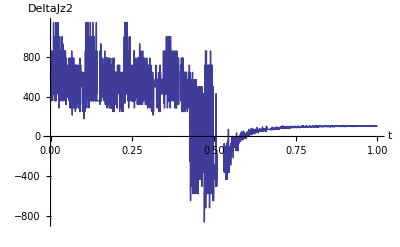

```mathematica
y[t_]=y[t]/.fullsolvey
Plot[y[t]/.{A->0.0559,B->-1.7525,C->715.0111,d->2500/4,γ->0.6085},{t,0,1},PlotRange->All,AxesLabel->{"t","DeltaJz2"}]
```